```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

## -1/3 < m < 0

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

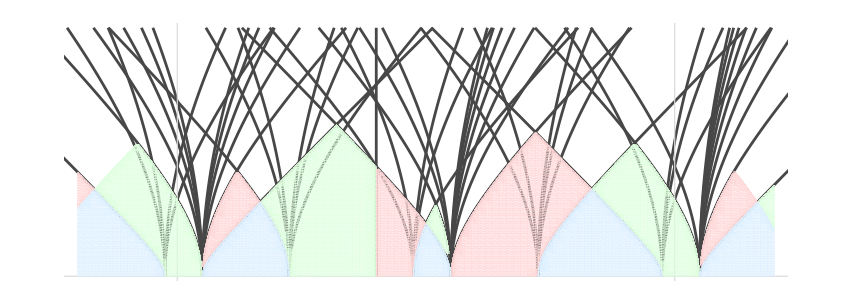

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=-1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

plt1=Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

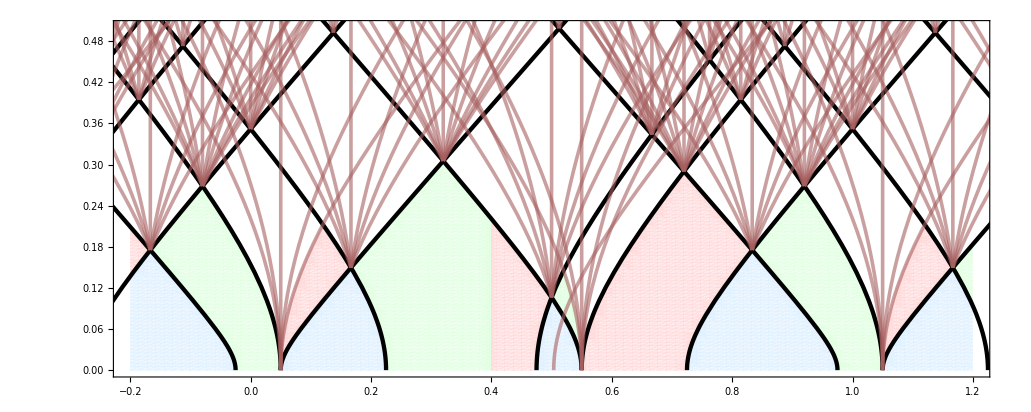

```mathematica
Show[domainI,domainII,domainBr,temp,AspectRatio->Automatic]
```

## 0 < m < 1/3

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{1,0},{2,1},{3,2},{4,2},{5,3}}

{{0,0},{1,1},{2,2},{3,2},{4,3}}

{{0,0},{1,1},{2,2},{3,2},{4,3}}

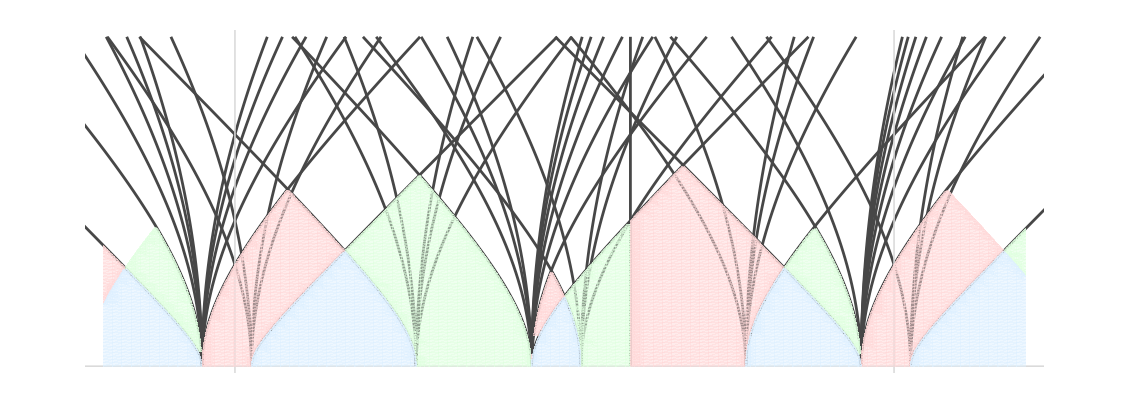

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

## 1/3 < m < 2/3

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{1,1},{2,1},{3,2},{4,3},{5,3}}

{{0,1},{1,1},{2,2},{3,3},{4,3}}

{{0,1},{1,1},{2,2},{3,3},{4,3}}

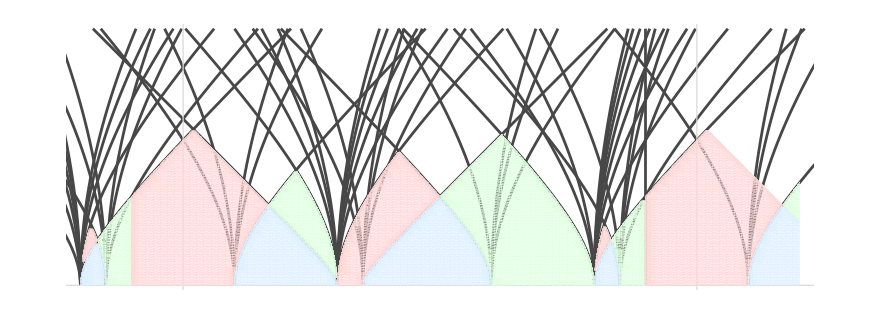

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=4/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

```mathematica
SpectralFlow[GV[0,-1,-1/2]/.repCh,{-3,-2}]
```

{0,0,-1,1/2}

```mathematica
Ch[0,0]-Ch[0,1]/.repCh
```

{0,0,-1,1/2}

```mathematica
With[{m=2/5},Flatten@Table[k+{m/4, (m+1)/4, (1-m)/2, (m+2)/4, m+1/2, (m+3)/4, 1-m/2}, {k,0,0}]]
```

{1/10,7/20,3/10,3/5,9/10,17/20,4/5}

```mathematica
{m/4, (m+1)/4, (1-m)/2, (m+2)/4, m+1/2, (m+3)/4, 1-m/2}
SortBy[%, #/.{m->2/5}&]
```

{m/4,(1+m)/4,(1-m)/2,(2+m)/4,1/2+m,(3+m)/4,1-m/2}

{m/4,(1-m)/2,(1+m)/4,(2+m)/4,1-m/2,(3+m)/4,1/2+m}

```mathematica
DSZ[Ch[1,1],-Ch[0,1]]/.repCh
```

2

```mathematica
DSZ[Ch[2,1],-Ch[0,1]]/.repCh
```

4

```mathematica
ChernToCh[2Ch[1,1]-Ch[0,1]/.repCh]
```

Ch[2,1]

```mathematica
DSZ[Ch[1,1],-Ch[2,2]]/.repCh
```

-3

```mathematica
DSZ[Ch[3,2],-Ch[2,2]]/.repCh
```

2

```mathematica
SpectralFlow[{0,0,1,ch2},{3k,2k}]
```

{0,0,1,ch2+k}

## Redo

## -1/3 < m < 0

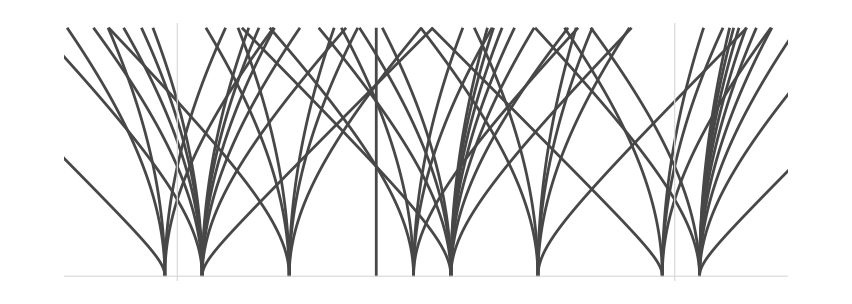

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
charges=With[{L=5},Join[charges,Table[GV[0,1,-1/2-k], {k,-L,L}]]];

With[{m=-1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];

(*(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];*)

plt1=Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
]
]
]
```

```mathematica
domsB=With[{m=-1/10},Table[QDomain[SpectralFlow[CollBridgeland/.repCh, {mf,Ceiling[(2mf+3m-1)/3]}], -1/10,PlotStyle->Directive[LightBlue, Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {mf,0,4}]];
```

```mathematica
domsAI=With[{m=-1/10},Table[QDomain[SpectralFlow[CollArcaraI/.repCh, {mf,Ceiling[(2mf+3m-3)/3]}], -1/10, PlotStyle->Directive[LightGreen, Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {mf,1,5}]];
```

```mathematica
domsAII=With[{m=-1/10},Table[QDomain[SpectralFlow[CollArcaraII/.repCh, {mf,Ceiling[(2mf+3m-1)/3]}], -1/10, PlotStyle->Directive[LightRed, Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {mf,0,4}]];
```

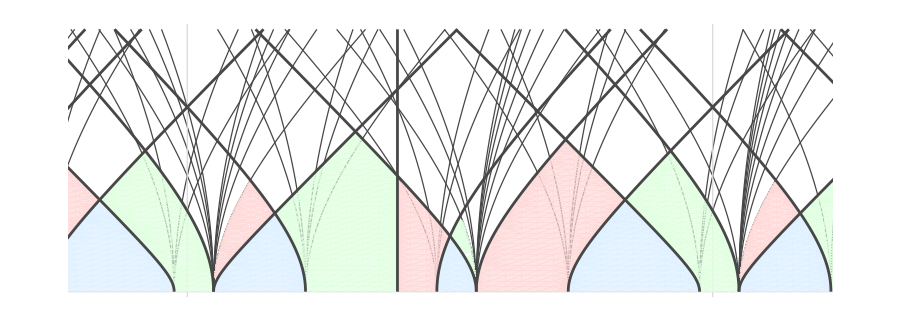

```mathematica
coll=CollInitial[[3]];
charges=With[{L=5},Flatten[Table[s gam/.{Ch[p_,q_]:>Ch[p+3k,q+2k]},{gam, coll},{k,-L,L},{s,{-1,1}}]]];
charges=With[{L=5},Join[charges,Table[GV[0,1,-1/2-k], {k,-L,L}]]];

othercharges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=-1/10, psi=0, xmin=-1, xmax=2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];

othercharges=Select[othercharges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&&!MemberQ[charges,#]&];
otherrays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, othercharges}];


plt1=Show[
ParametricPlot[otherrays, {t,0,0.5},
PlotStyle->Directive[Thickness[.001],RGBColor[0.28, 0.28, 0.28], Opacity[.8]]
],
domsB,
domsAI,
domsAII,
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28]
],
PlotRange->{{-0.2,1.2},{0,0.5}},
AspectRatio->Automatic,
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
]
]
```

```mathematica
ReZLV[{r_,df_,db_,ch2_},{s_,t_},m_]:=-ch2-db m+df m+(m^2 r)/2+(db+2 df-m r) s-4 r s^2+4 r t^2;
QConditions[Coll_,m_,{s_,t_}]:=And@@(ReZLV[#,{s,t},m]<0&/@Coll);
```

```mathematica
ClearAll[QDomain];
Options[QDomain]=Options[RegionPlot];
QDomain[Coll_, m_, opt___:OptionsPattern[]]:=RegionPlot[QConditions[Coll, m, {s, t}], {s, -1, 2}, {t,0, 1}, opt];
```

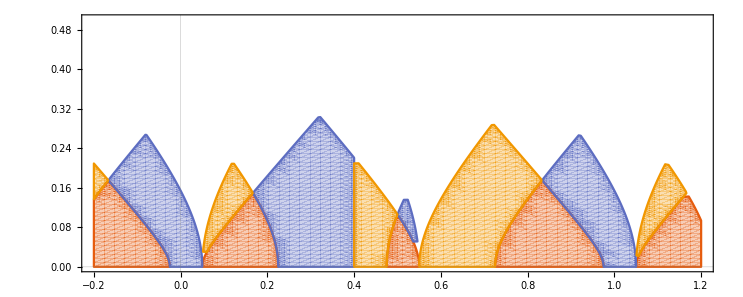

```mathematica
With[{m=-1/10},
RegionPlot[
{Or@@Table[QDomain[SpectralFlow[CollBridgeland/.repCh, {mf,Ceiling[(2mf+3m-1)/3]}], m, {s,t}], {mf,-1,4}],
Or@@Table[QDomain[SpectralFlow[CollArcaraI/.repCh, {mf,Ceiling[(2mf+3m-3)/3]}], m, {s,t}], {mf,-1,4}],
Or@@Table[QDomain[SpectralFlow[CollArcaraII/.repCh, {mf,Ceiling[(2mf+3m-1)/3]}], m, {s,t}], {mf,-1,4}]
},
{s,-0.2, 1.2},{t,0,0.5},
PlotTheme->"Scientific",
PlotPoints->60,
AspectRatio->Automatic
]
]
```